```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/RESULTS_tom_22Aug17/phonon_dos/fren-70_phon_dos"];
phDOSfiles={"1.total_dos.dat","2.total_dos.dat","3.total_dos.dat","4.total_dos.dat","5.total_dos.dat","6.total_dos.dat","7.total_dos.dat","8.total_dos.dat","9.total_dos.dat","10.total_dos.dat","11.total_dos.dat"};
fren70dos=Table[ReadList[phDOSfiles[[i]],{Number,Number}],{i,1,Length@phDOSfiles}];
```

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/RESULTS_tom_22Aug17/phonon_dos/cvac_phon_dos"];
cvac=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{40,0.0},{42,0.0}}}],2],{i,1,9}];
SetDirectory["/Volumes/MicroSD/Dropbox/RESULTS_tom_22Aug17/phonon_dos/perf_phon_dos"];
perf=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{40,0.0},{42,0.0}}}],2],{i,1,9}];
SetDirectory["/Volumes/MicroSD/Dropbox/RESULTS_tom_22Aug17/phonon_dos/fren-1126_phon_dos"];
fren1126=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{40,0.0},{42,0.0}}}],2],{i,1,Length@phDOSfiles}];
SetDirectory["/Volumes/MicroSD/Dropbox/RESULTS_tom_22Aug17/phonon_dos/fren-129_phon_dos"];
fren129=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{40,0.0},{42,0.0}}}],2],{i,1,Length@phDOSfiles}];
SetDirectory["/Volumes/MicroSD/Dropbox/RESULTS_tom_22Aug17/phonon_dos/fren-142_phon_dos"];
fren142=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{40,0.0},{42,0.0}}}],2],{i,1,Length@phDOSfiles}];
SetDirectory["/Volumes/MicroSD/Dropbox/RESULTS_tom_22Aug17/phonon_dos/fren-174_phon_dos"];
fren174=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{40,0.0},{42,0.0}}}],2],{i,1,Length@phDOSfiles}];
SetDirectory["/Volumes/MicroSD/Dropbox/RESULTS_tom_22Aug17/phonon_dos/fren-70_phon_dos"];
fren70=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{40,0.0},{42,0.0}}}],2],{i,1,Length@phDOSfiles}];
```

```mathematica
names={"perf","fren129","fren142","fren70","fren174","fren1126","cvac"};
objects={perf,fren129,fren142,fren70,fren174,fren1126,cvac};
alatts={4.575,4.600,4.625,4.6583,4.685,4.730,4.759,4.801,4.850,4.875,4.900};
vols=(alatts*2)^3/64;
```

```mathematica
fren1126Data=Table[Table[Flatten[{fren1126[[j]][[i]][[1]],vols[[j]],fren1126[[j]][[i]][[2]]}],{i,1,Length@fren1126[[j]]}],{j,1,Length@vols}];
fren1126Data2D=Table[Table[Flatten[{fren1126[[j]][[i]][[1]],fren1126[[j]][[i]][[2]]+10*vols[[j]]}],{i,1,Length@fren1126[[j]]}],{j,1,Length@vols}];
data=Table[Table[Table[Flatten[{objects[[k]][[j]][[i]][[1]],vols[[j]],objects[[k]][[j]][[i]][[2]]}],{i,1,Length@objects[[k]][[j]]}],{j,1,Length@objects[[k]]}],{k,1,Length@objects}];
data2D=Table[Table[Table[Flatten[{objects[[k]][[j]][[i]][[1]],objects[[k]][[j]][[i]][[2]]+10*vols[[j]]}],{i,1,Length@objects[[k]][[j]]}],{j,1,Length@objects[[k]]}],{k,1,Length@objects}];
```

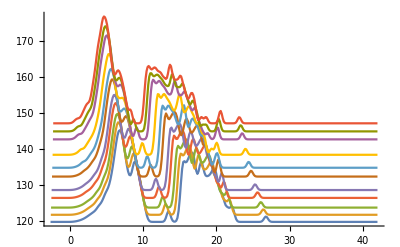

```mathematica
ListPointPlot3D@fren1126Data;
ListLinePlot@fren1126Data2D
```

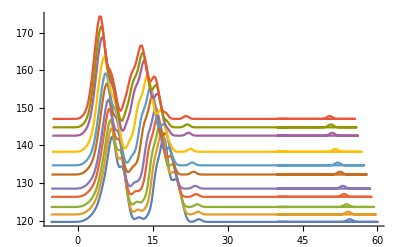

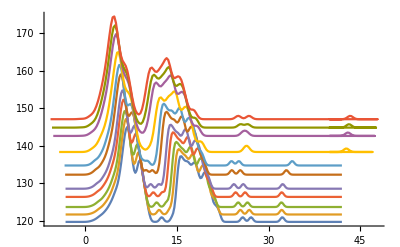

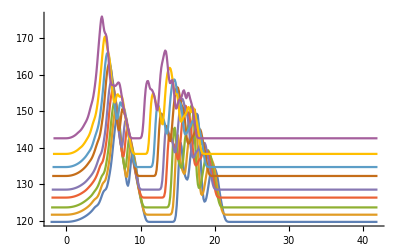

```mathematica
ListLinePlot@data2D[[4]]
ListLinePlot@data2D[[5]]
ListLinePlot@data2D[[-1]]
```

#### Plot3d

```mathematica
plotStyle3D={BoxRatios->{1,1,1},FillingStyle->Directive[Thickness[1],Orange,Thin,Opacity[0.1]],Filling->Bottom,PlotTheme->"Scientific",AxesLabel->{Style["ω (THz)",18,Black],Style["Volume \n(Å^3/atom) ",18,Black],Style["DOS ",18,Black]" \n(1/THz)  "},AxesStyle->Directive[18,Black,Thickness[0.004]],Boxed->False,BoxStyle->Directive[Thickness[0.00001],Dashing[0.02]],PlotStyle->Directive[Black,PointSize[0.006]],ImageSize->650,ViewPoint->{-5005,-100000,15}};
ListPointPlot3D[fren1126Data,Evaluate@plotStyle3D]/.Point[a___]:>{Thickness[0.004],Line[a]};
```

#### Plot2D

36

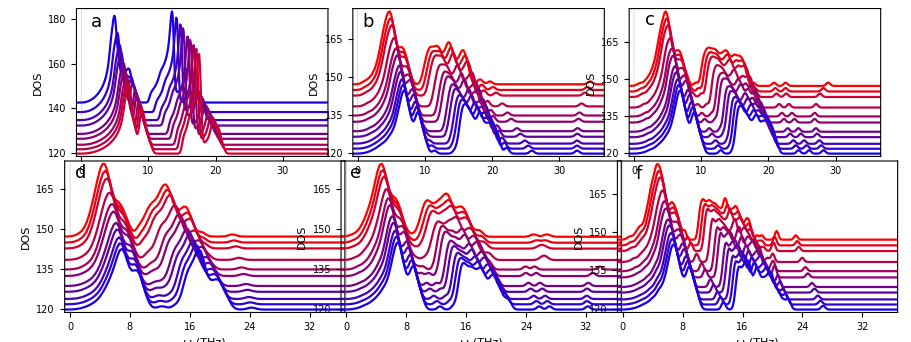

```mathematica
par=36
plotStyle={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{True,None},FrameLabel->{Style["ω (THz)",18,Black],Style["DOS ",18,Black]},PlotStyle->Reverse@Table[Blend[{Blue,Red},i/11],{i,1,11}],FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->450,PlotRange->{{0,30},Automatic}};

plotStyle1={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{Automatic,Automatic},FrameTicksStyle->{0.1,0.1},FrameLabel->{Style["",18,Black],Style["DOS ",18,Black]},PlotStyle->Table[Blend[{Blue,Red},i/11],{i,1,11}],FrameStyle->Reverse@Directive[18,Black,Thickness[0.006]],ImageSize->350,PlotRange->{{0,par},Automatic},PlotLabels->{Placed[Style["a",18,Black],{0.09,0.88}]}};




plotStyle2={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{Automatic,Automatic},FrameTicksStyle->{0.1,0.1},FrameLabel->{Style["",18,Black],Style["DOS",18,Opacity[0]]},PlotStyle->Reverse@Table[Blend[{Blue,Red},i/11],{i,1,11}],FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->350,PlotRange->{{0,par},Automatic},PlotLabels->{Placed[Style["b",18,Black],{0.113,0.86}]}};
plotStyle3={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{Automatic,Automatic},FrameTicksStyle->{0.1,0.1},FrameLabel->{Style["",18,Black],Style["DOS",18,Opacity[0]]},PlotStyle->Reverse@Table[Blend[{Blue,Red},i/11],{i,1,11}],FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->350,PlotRange->{{0,par},Automatic},PlotLabels->{Placed[Style["c",18,Black],{0.128,0.88}]}};
plotStyle4={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{Automatic,Automatic},FrameTicksStyle->{0.1,Automatic},FrameLabel->{Style["ω (THz)",18,Black],Style["DOS ",18,Black]},PlotStyle->Reverse@Table[Blend[{Blue,Red},i/11],{i,1,11}],FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->390,PlotRange->{{0,par},Automatic},PlotLabels->{Placed[Style["d",18,Black],{0.106,0.87}]}};


plotStyle5={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{Automatic,Automatic},FrameTicksStyle->{0.1,Automatic},FrameLabel->{Style["ω (THz)",18,Black],Style["DOS",18,Opacity[0]]},PlotStyle->Reverse@Table[Blend[{Blue,Red},i/11],{i,1,11}],FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->390,PlotRange->{{0,par},Automatic},PlotLabels->{Placed[Style["e",18,Black],{0.13,0.88}]}};
plotStyle6={AspectRatio->0.5,Frame->True,PlotTheme->"Scientific",FrameTicks->{Automatic,Automatic},FrameTicksStyle->{0.1,Automatic},FrameLabel->{Style["ω (THz)",18,Black],Style["DOS",18,Opacity[0]]},PlotStyle->Reverse@Table[Blend[{Blue,Red},i/11],{i,1,11}],FrameStyle->Directive[18,Black,Thickness[0.006]],ImageSize->390,PlotRange->{{0,par},Automatic},PlotLabels->{Placed[Style["f",18,Black],{0.1,0.87}]}};
plotStyles={plotStyle1,plotStyle2,plotStyle3,plotStyle4,plotStyle5,plotStyle6};

plots=Table[ListLinePlot[Reverse@data2D[[i]],Evaluate@plotStyles[[i]]],{i,1,6}];
gridplot=GraphicsGrid[{plots[[1;;3]],plots[[4;;6]]},Spacings->{-90,-30}]
```

```mathematica
Export["/Users/tom/Documents/Lyx_documents/Intrinsic_defect_ZrC/images/phon-dos.pdf",gridplot]
```

/Users/tom/Documents/Lyx_documents/Intrinsic_defect_ZrC/images/phon-dos.pdf

```mathematica
Log[1]
```

0

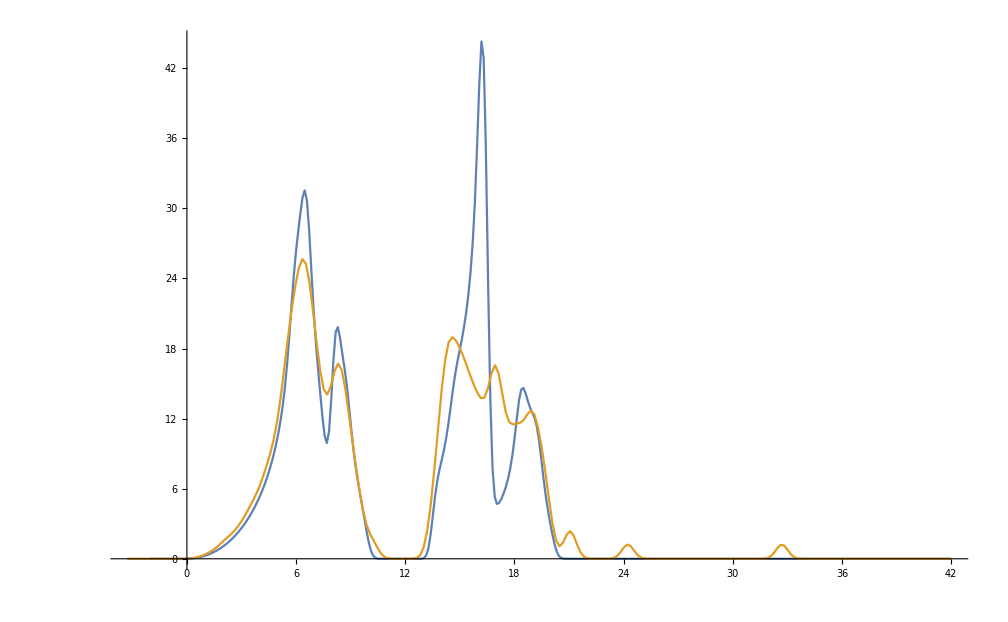

```mathematica
ListLinePlot[{perf[[4]],fren129[[4]]}]
```

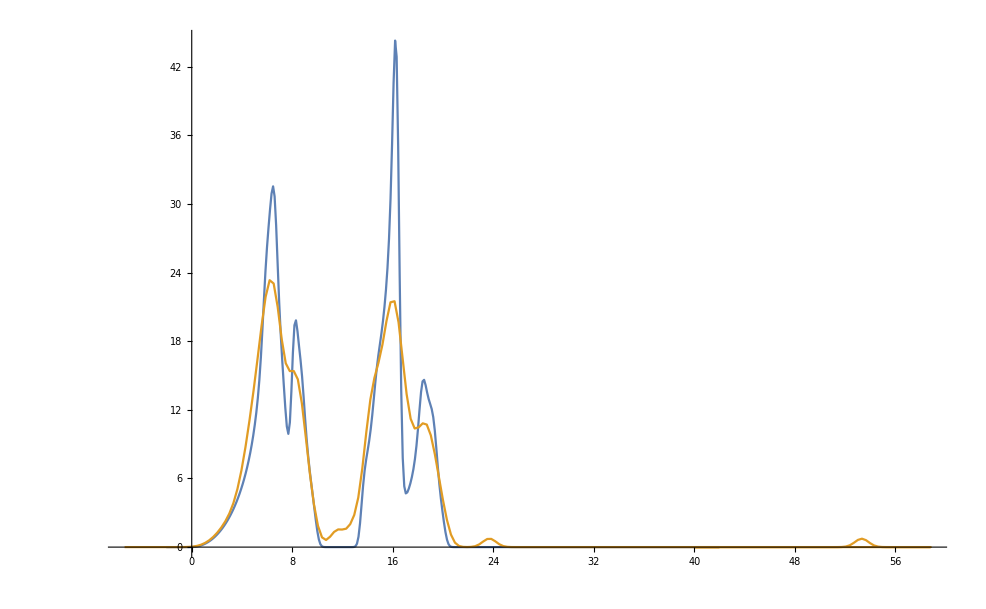

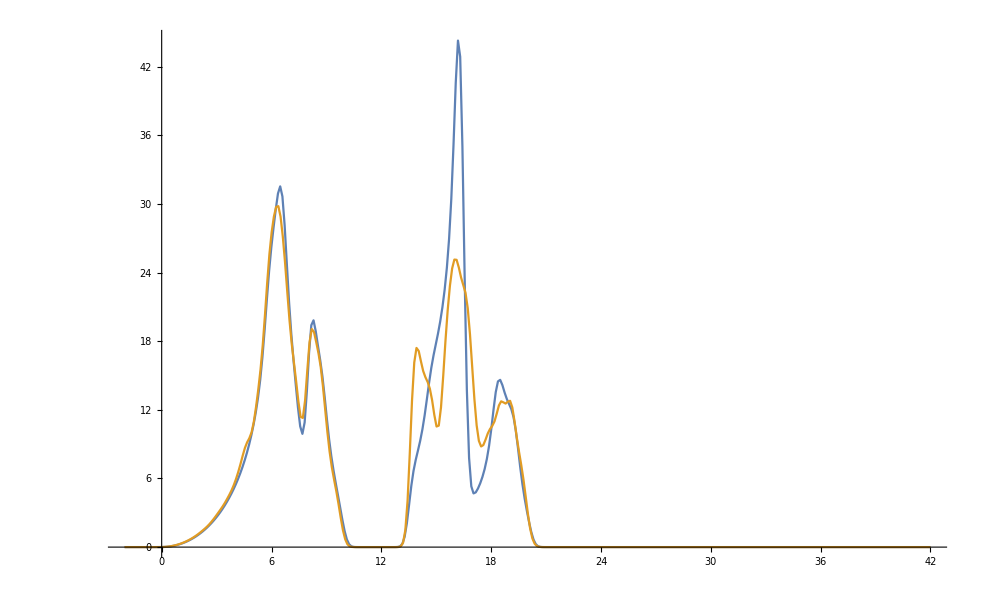

```mathematica
ListLinePlot[{perf[[4]],fren70[[4]]}]
```

```mathematica
pInt=Interpolation[perf[[4]]];
pFren129=Interpolation[fren129[[4]]];
pFren142=Interpolation[fren142[[4]]];
pFren70=Interpolation[fren70[[4]]];
pFren174=Interpolation[fren174[[4]]];
pFren1126=Interpolation[fren1126[[4]]];
pcvac=Interpolation[cvac[[4]]];
gmean[arg_,min_,max_]:=Exp[Integrate[Log[x]*arg[x],{x,min,max}]/Integrate[arg[x],{x,min,max}]]//N
mean[arg_,min_,max_]:=Integrate[x*arg[x],{x,min,max}]/Integrate[arg[x],{x,min,max}]//N
n[arg_,min_,max_]:=NIntegrate[arg[x],{x,min,max}]//N
```

```mathematica
ints[[1]];
```

Part::partd: Part specification ints⟦1⟧ is longer than depth of object.

```mathematica
ints=Table[Table[Interpolation[objects[[i]][[j]]],{j,1,objects[[i]]//Length}],{i,1,7}];
```

```mathematica
Table[Table[Integrate[ints[[j]][[i]][x],{x,-0.25,58}],{i,1,Length@ints[[j]]}],{j,1,7}]//TableForm
```

InterpolatingFunction::dmvali: The integration endpoint 58 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmvali will be suppressed during this calculation.

192. | 192. | 192. | 192. | 192. | 192. | 192. | 192. | 192. |  | 
191.999 | 191.999 | 191.999 | 191.999 | 191.999 | 191.999 | 191.999 | 191.999 | 191.998 | 191.998 | 191.996
192. | 192. | 192. | 192. | 192. | 192. | 192. | 192. | 191.999 | 191.999 | 191.985
191.996 | 191.996 | 191.996 | 191.996 | 191.996 | 191.996 | 191.995 | 191.995 | 191.994 | 191.993 | 191.992
192. | 192. | 192. | 191.999 | 191.999 | 191.999 | 191.999 | 192.006 | 191.956 | 191.934 | 191.889
192. | 192. | 192. | 192. | 192. | 192. | 192. | 192. | 192. | 192. | 192.
189. | 189. | 189. | 189. | 189. | 189. | 189. | 189. | 189. |  |

```mathematica
(*U3 4.9 is imaginary strongly at X, 4.801 is very soft, but all postive*)
(*U3 4.759 is all positive. 5 defect modes clear *)
(*U2 all fine*)
(*U2 all fine*)
```

```mathematica
cvac;
```

#### Cvac gMEAN

```mathematica
-31Log[gmean[pcvac,12,22]]+32Log[gmean[pInt,12,22]]
```

2.87323

```mathematica
gmean[pcvac,0,12]/gmean[pInt,0,12]
gmean[pcvac,12,22]/gmean[pInt,12,22]
```

0.990027

0.997518

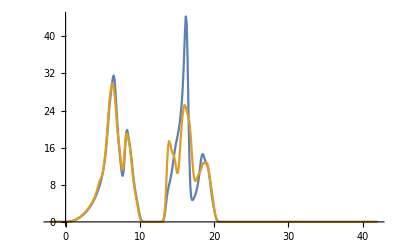

0.320722

0.0795103

0.884204

```mathematica
ListLinePlot[{perf[[4]],cvac[[4]]}]
-32Log[gmean[pcvac,0,12]/gmean[pInt,0,12]]
-32Log[gmean[pcvac,12,22]/gmean[pInt,12,22]]
-64Log[gmean[pcvac,0,22]/gmean[pInt,0,22]]
```

```mathematica
list1={1,4,5,6}
list2={10,15,20,21}
GeometricMean@list1//N
GeometricMean@list2//N
GeometricMean@Flatten@{list1,list2}//N
GeometricMean@{3.3097509196468726,14.422495703074084}
GeometricMean@Flatten@{list2/list1}//N
GeometricMean@Flatten@{list2*list1}//N
```

{1,4,5,6}

{10,15,20,21}

3.30975

15.8429

7.24128

6.90904

4.78674

52.4361

```mathematica
15.84291664941221/3.3097509196468726
15.84291664941221*3.3097509196468726
```

4.78674

52.4361

```mathematica
-32Log[(gmean[pcvac,0,12]*gmean[pcvac,12,22])/(gmean[pInt,0,12]*gmean[pInt,12,22])]
```

0.400232

Fren129

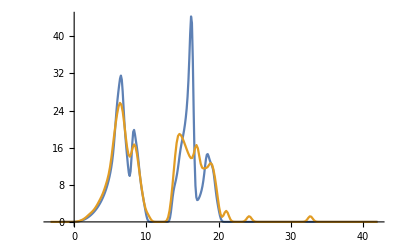

NIntegrate::nlim: x = y is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{y→10.7752}

0.560128

-0.477983

0.394923

```mathematica
Fren129
ListLinePlot[{perf[[4]],fren129[[4]]}]
rule=FindRoot[NIntegrate[pFren142[x],{x,0,y}]-NIntegrate[pFren142[x],{x,y,35}]==0,{y,12}]
-32Log[gmean[pFren129,0,y/.rule]/gmean[pInt,0,12]]
-32Log[gmean[pFren129,y/.rule,35]/gmean[pInt,12,22]]
-64Log[gmean[pFren129,0,35]/gmean[pInt,0,22]]
```

Fren142

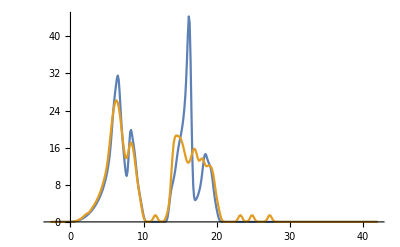

NIntegrate::nlim: x = y is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{y→10.7752}

0.709974

-0.468857

0.241205

```mathematica
Fren142
ListLinePlot[{perf[[4]],fren142[[4]]}]
rule=FindRoot[NIntegrate[pFren142[x],{x,0,y}]-NIntegrate[pFren142[x],{x,y,35}]==0,{y,12}]
-32Log[gmean[pFren142,0,y/.rule]/gmean[pInt,0,12]]
-32Log[gmean[pFren142,y/.rule,35]/gmean[pInt,12,22]]
-64Log[gmean[pFren142,0,35]/gmean[pInt,0,22]]
```

Fren70

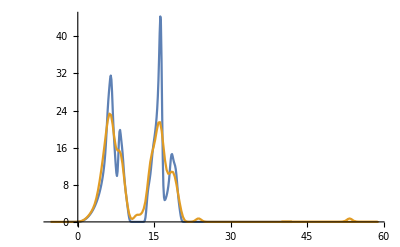

NIntegrate::nlim: x = y is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{y→10.5873}

0.817316

-0.0534032

0.764002

```mathematica
Fren70
ListLinePlot[{perf[[4]],fren70[[4]]}]
rule=FindRoot[NIntegrate[pFren70[x],{x,0,y}]-NIntegrate[pFren70[x],{x,y,55}]==0,{y,12}]
-32Log[gmean[pFren70,0,y/.rule]/gmean[pInt,0,12]]
-32Log[gmean[pFren70,y/.rule,55]/gmean[pInt,12,22]]
-64Log[gmean[pFren70,0,55]/gmean[pInt,0,22]]
```

Fren174

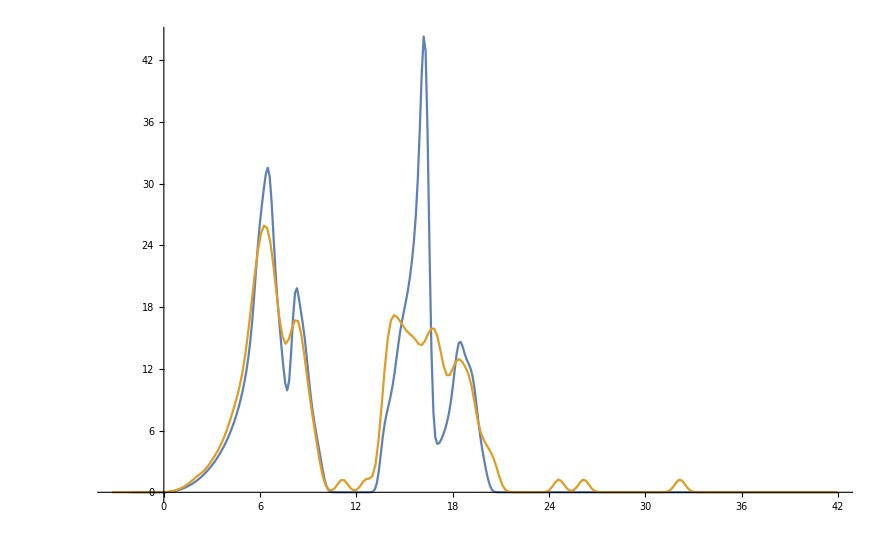

NIntegrate::nlim: x = y is not a valid limit of integration.

InterpolatingFunction::dmvali: The integration endpoint 55 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

NIntegrate::nlim: x = y is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

InterpolatingFunction::dmvali: The integration endpoint 55 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmvali will be suppressed during this calculation.

{y→10.4011}

0.844944

-0.377174

0.467858

```mathematica
Fren174
ListLinePlot[{perf[[4]],fren174[[4]]}]
rule=FindRoot[NIntegrate[pFren174[x],{x,0,y}]-NIntegrate[pFren174[x],{x,y,55}]==0,{y,10}]
-32Log[gmean[pFren174,0,y/.rule]/gmean[pInt,0,12]]
-32Log[gmean[pFren174,y/.rule,35]/gmean[pInt,12,22]]
-64Log[gmean[pFren174,0,35]/gmean[pInt,0,22]]
```

Fren1126

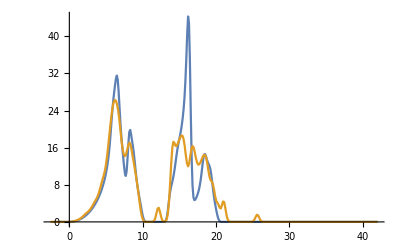

NIntegrate::nlim: x = y is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{y→11.2785}

0.82142

-0.40226

0.419249

```mathematica
Fren1126
ListLinePlot[{perf[[4]],fren1126[[4]]}]
rule=FindRoot[NIntegrate[pFren1126[x],{x,0,y}]-NIntegrate[pFren1126[x],{x,y,40}]==0,{y,12}]
-32Log[gmean[pFren1126,0,y/.rule]/gmean[pInt,0,12]]
-32Log[gmean[pFren1126,y/.rule,35]/gmean[pInt,12,22]]
-64Log[gmean[pFren1126,0,35]/gmean[pInt,0,22]]
```

```mathematica
gmean[pInt,12,20.7]
gmean[pFren129,12,20.7]
-64Log[gmean[pFren129,0,50]/gmean[pInt,0,35]]
```

16.3824

16.3671

InterpolatingFunction::dmvali: The integration endpoint 50 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

0.394923

```mathematica
gmean[pInt,0,35]
gmean[pFren70,-3,57]
gmean[pFren70,0,57]
```

10.2119

10.0301+0.0513697 ⅈ

10.0688

```mathematica
pFren70
```

InterpolatingFunction[{{-7.25057, 58.817}}, <>]

```mathematica
-64Log[gmean[pFren70,0,57]/gmean[pInt,0,35]]
-64Log[gmean[pFren70*192/191,0,57]/gmean[pInt,0,35]]
```

0.903559

NIntegrate::inumr: The integrand (192/191 InterpolatingFunction[{{-7.25057,58.817}},{5,7,0,{203},{4},0,0,0,0,Automatic,{},{},False},«1»,{Developer`PackedArrayForm,{0,«49»,«154»},{0.,0.,0.,0.,0.,0.,0.,1.2×10^-9,3.54×10^-8,7.62×10^-7,0.0000115651,0.000124006,0.00094154,0.00507798,0.0195377,0.053966,0.10807,0.159517,0.178645,«13»,4.12616,5.38362,7.01856,8.98917,11.1998,13.6591,16.4289,19.3298,21.7675,22.8998,22.1537,19.8326,17.1771,15.5125,15.0842,14.8545,13.6457,11.2261,«153»}},{Automatic}])[x] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,57}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

-64 Log[0.0979245 2.71828^(NIntegrate[Log[x] (192 InterpolatingFunction[{{-7.25057, 58.817}}, <>])/191[x],{x,0,57}]/NIntegrate[(192 InterpolatingFunction[{{-7.25057, 58.817}}, <>])/191[x],{x,0,57}])]

```mathematica
names
objects;
```

{perf,fren129,fren142,fren70,fren174,fren1126}

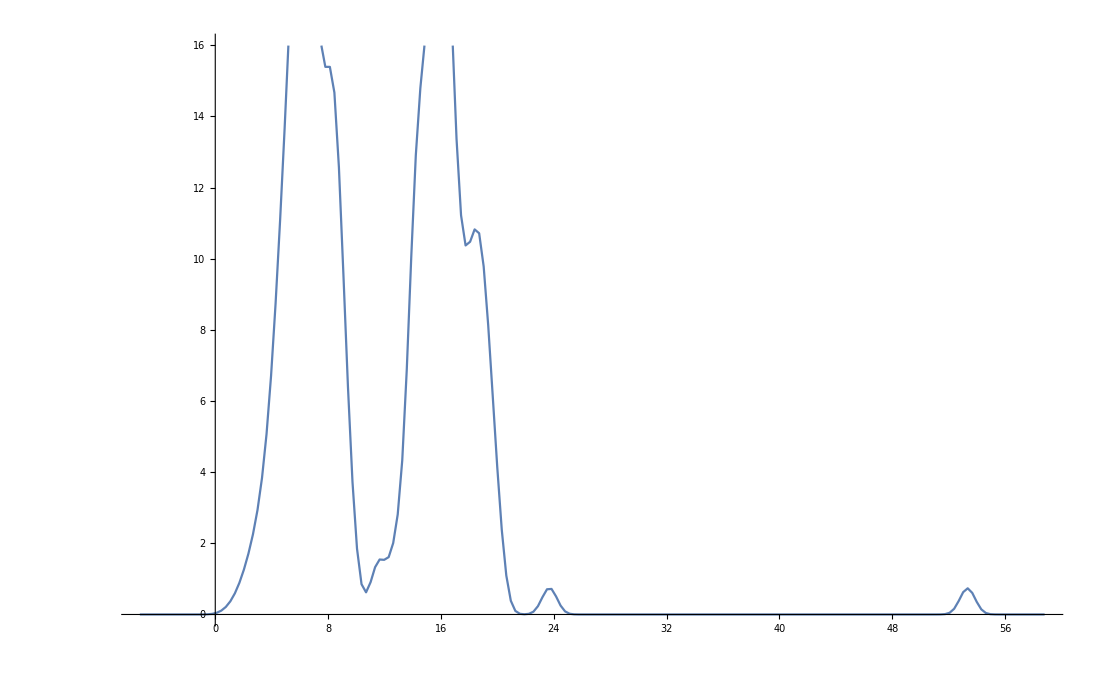

```mathematica
ListLinePlot[ints[[4]][[4]]]
```

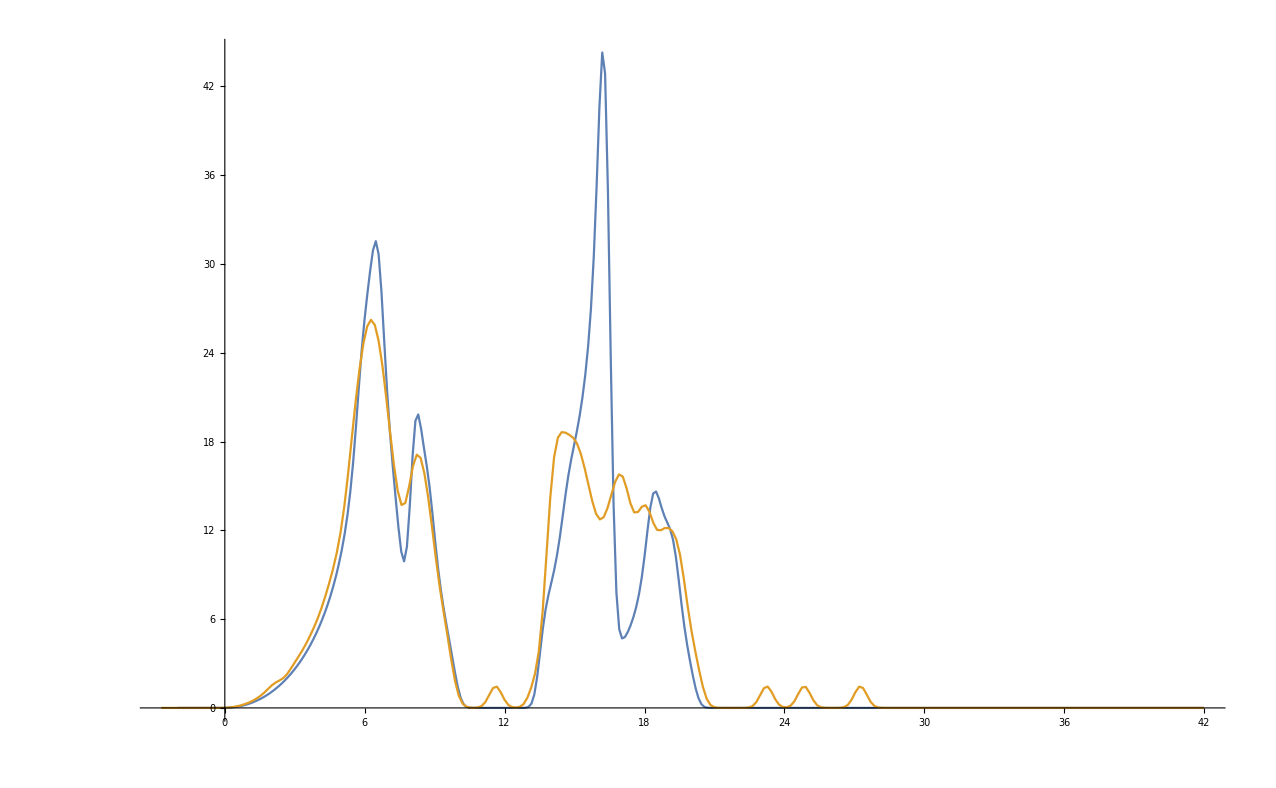

```mathematica
ListLinePlot[Table[ints[[i]][[4]],{i,1,3,2}]]
```

```mathematica
gmean[pInt,12.5,22]
gmean[pFren142,12.5,22]
n[pInt,12.5,22]
n[pFren142,12.5,22]
n[pFren142,12.5,22]/n[pInt,12.5,22]
```

16.3824

16.4672

96.

91.9993

0.958326

```mathematica
n[pInt,0,12.5]
n[pFren142,0,12.5]
n[pInt,0,12.5]/n[pFren142,0,12.5]
```

95.9994

96.999

0.989695

```mathematica
ints//Dimensions
objects//Dimensions
```

{6}

{6}

```mathematica
nn=Table[Table[n[ints[[j]][[i]],0,objects[[j]][[i]][[-1]][[1]]]/192,{i,1,objects[[j]]//Length}],{j,2,6}]
```

{{0.999987,0.999986,0.999985,0.999984,0.999982,0.999979,0.999976,0.99997,0.999956,0.999944,0.999913},{0.999992,0.999992,0.999992,0.999991,0.999991,0.999989,0.999988,0.999984,0.999976,0.999964,0.999786},{0.994746,0.994744,0.994743,0.99474,0.994738,0.994733,0.994729,0.994721,0.994706,0.994694,0.994676},{0.999988,0.999988,0.999987,0.999986,0.999984,0.99998,0.999974,0.995046,0.994494,0.99418,0.993987},{0.999994,0.999993,0.999993,0.999993,0.999993,0.999992,0.999991,0.999989,0.999983,0.999981,0.999974}}

```mathematica
Table[Join[{names[[j]]},Table[n[ints[[j]][[i]],0,objects[[j]][[i]][[-1]][[1]]]/192,{i,1,objects[[j]]//Length}]],{j,1,6}]//TableForm
```

perf | 0.999997 | 0.999997 | 0.999997 | 0.999997 | 0.999997 | 0.999997 | 0.999997 | 0.999997 | 0.999996 |  | 
fren129 | 0.999987 | 0.999986 | 0.999985 | 0.999984 | 0.999982 | 0.999979 | 0.999976 | 0.99997 | 0.999956 | 0.999944 | 0.999913
fren142 | 0.999992 | 0.999992 | 0.999992 | 0.999991 | 0.999991 | 0.999989 | 0.999988 | 0.999984 | 0.999976 | 0.999964 | 0.999786
fren70 | 0.994746 | 0.994744 | 0.994743 | 0.99474 | 0.994738 | 0.994733 | 0.994729 | 0.994721 | 0.994706 | 0.994694 | 0.994676
fren174 | 0.999988 | 0.999988 | 0.999987 | 0.999986 | 0.999984 | 0.99998 | 0.999974 | 0.995046 | 0.994494 | 0.99418 | 0.993987
fren1126 | 0.999994 | 0.999993 | 0.999993 | 0.999993 | 0.999993 | 0.999992 | 0.999991 | 0.999989 | 0.999983 | 0.999981 | 0.999974

```mathematica
deltaS=Table[Table[-64Log[gmean[ints[[1+j]][[i]],0,objects[[1+j]][[i]][[-1]][[1]]]/(gmean[ints[[1]][[i]],0,objects[[1]][[i]][[-1]][[1]]])],{i,1,9}],{j,1,5}]
```

{{0.676415,0.613465,0.530735,0.394923,0.294088,0.0754326,-0.069526,-0.300943,-0.601219},{0.512438,0.452401,0.375047,0.241205,0.13277,-0.0813843,-0.230705,-0.467484,-0.793351},{1.50965,1.4774,1.4247,1.32137,1.24184,1.08903,0.988462,0.847768,0.684815},{0.68544,0.639307,0.574367,0.467858,0.389147,0.263397,0.273234,0.675694,0.362452},{0.657388,0.610209,0.542202,0.419249,0.312032,0.0947849,-0.0544036,-0.301704,-0.656519}}

```mathematica
Transpose[deltaS]
```

{{0.676415,0.512438,1.50965,0.68544,0.657388},{0.613465,0.452401,1.4774,0.639307,0.610209},{0.530735,0.375047,1.4247,0.574367,0.542202},{0.394923,0.241205,1.32137,0.467858,0.419249},{0.294088,0.13277,1.24184,0.389147,0.312032},{0.0754326,-0.0813843,1.08903,0.263397,0.0947849},{-0.069526,-0.230705,0.988462,0.273234,-0.0544036},{-0.300943,-0.467484,0.847768,0.675694,-0.301704},{-0.601219,-0.793351,0.684815,0.362452,-0.656519}}

```mathematica
Table[Join[{names[[i+1]]},deltaS[[i]]],{i,1,5}]//TableForm
```

fren129 | 0.676415 | 0.613465 | 0.530735 | 0.394923 | 0.294088 | 0.0754326 | -0.069526 | -0.300943 | -0.601219
fren142 | 0.512438 | 0.452401 | 0.375047 | 0.241205 | 0.13277 | -0.0813843 | -0.230705 | -0.467484 | -0.793351
fren70 | 1.50965 | 1.4774 | 1.4247 | 1.32137 | 1.24184 | 1.08903 | 0.988462 | 0.847768 | 0.684815
fren174 | 0.68544 | 0.639307 | 0.574367 | 0.467858 | 0.389147 | 0.263397 | 0.273234 | 0.675694 | 0.362452
fren1126 | 0.657388 | 0.610209 | 0.542202 | 0.419249 | 0.312032 | 0.0947849 | -0.0544036 | -0.301704 | -0.656519

```mathematica
deltaSAt=deltaS/64
```

{{0.010569,0.0095854,0.00829274,0.00617067,0.00459512,0.00117863,-0.00108634,-0.00470223,-0.00939404},{0.00800684,0.00706877,0.00586012,0.00376883,0.00207453,-0.00127163,-0.00360476,-0.00730444,-0.0123961},{0.0235882,0.0230843,0.0222609,0.0206465,0.0194038,0.0170162,0.0154447,0.0132464,0.0107002},{0.01071,0.00998917,0.00897448,0.00731029,0.00608043,0.00411558,0.00426927,0.0105577,0.00566331},{0.0102717,0.00953451,0.0084719,0.00655076,0.0048755,0.00148101,-0.000850056,-0.00471413,-0.0102581}}

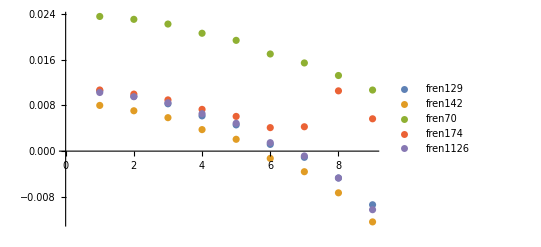

```mathematica
ListPlot[deltaSAt,PlotLegends->names[[2;;-1]]]
```

```mathematica
D[D[10x^8*7,x],x]
D[D[10x^8,x],x]*7
```

3920 x^6

3920 x^6